```mathematica
Aerospace[] :=(
ClearAll[trueb, truee0, trueCD0, trueW1, trueS, trueTA, trueρ∞SL, trueh, trueVlimit, trueSFC];
ClearAll[AR, e0, CD0, W1, S, TA,Vlimit, SFC];
ClearAll[ρ∞, σ, TAR, CL, CD, TR, PR, PA, PlotT, PlotP, Vmax, Vstall, LDmaxV, RCmax, Info, Aligned, PlotRC, RC, A, IRC, TimeToClimb, PlotTTC,PlotIRC];
trueb = false;
truee0 = false;
trueCD0 = false;
trueW1 = false;
trueS = false;
trueTA = false;
trueρ∞SL = false;
trueh = false;
trueVlimit = false;
trueW0 = false;
trueSFC = false;
While[trueb == false,(b = Input["Input Wing Span (greater than 0)", 30]; If[b > 0,trueb = true, trueb = false])];
While[truee0 == false,(e0 =  Input["Input Oswald Efficiency Factor (between 0 and 1)", .875]; If[e0 > 0 && e0 ≤ 1,truee0 = true, truee0 = false])];
While[trueCD0 == false, (CD0 = Input["Input Zero-Lift Drag (between 0 and 1)", .013125]; If[CD0 > 0 && CD0 ≤ 1,trueCD0= true, trueCD0 = false])];
While[trueSFC == false, (SFC =  Input["Specific Fuel Consumption (lb/hr/lb)",0.78]; If[SFC > 0,trueSFC = true, trueSFC = false])];
While[trueW1 == false, (W1 =  Input["Input Empty Weight (greater than 0)", 12500]; If[W1 > 0,trueW1 = true, trueW1 = false])];
While[trueS == false, (S = Input["Input Wing Area (greater than 0)", 275]; If[S> 0,trueS = true, trueS = false])];
While[trueTA == false, (TA = Input["Input Thrust Available (greater than 0)", 5227]; If[TA > 0,trueTA = true, trueTA = false])];
While[trueVlimit == false, (Vlimit = Input["Input the Upper Velocity Limit for the Graph (greater than 0)", 1000]; If[Vlimit > 0,trueVlimit = true, trueVlimit= false])];
While[trueW0 == false, (W0= Input["Input the Upper Velocity Limit for the Graph (greater than 0)", 1.39*W1]; If[W0> 0,trueW0 = true, trueW0= false])];
ρ∞array = {.002377, .002048, .001756, .001496, .001267, .001066, .000891, .000738, .000587, .000462, .000364, .000287, .000226};
αarray = {1116.4, 1097.1, 1077.4, 1057.4, 1036.9, 1016.1, 994.8, 973.1, 968.1, 968.1, 968.1, 968.1, 968.1};
ρ∞[h_] := ρ∞array[[((h+5000)/5000)]];
α[h_] := αarray[[((h+5000)/5000)]];
c = S/b;
AR = b/c;
Print["Aspect Ratio is ", AR//N];
σ[h_] := ρ∞[h]/ρ∞[0];
W0[W1_] := 1.39*W1;
Print["Max Takeoff Weight is " , W0];
TAR[h_] := TA*σ[h]; 
CL[V_, h_] := W0/(.5*ρ∞[h]*V^2*S);
CD[V_, h_] := CD0+((CL[V, h]^2)/(Pi*e0*AR));
TR[V_, h_] := W0/(CL[V, h]/CD[V,h]);
PR[V_, h_] := TR[V, h]*V;
PA[V_, h_] := TAR[h]*V;
Vmax[h_] := Solve[TR[V, h] == TAR[h], V][[4,1,2]];
Vstall[h_] := Solve[TR[V, h] == TAR[h], V][[3,1,2]];
LDmaxV[h_] :=Solve[D[PR[V, h],V] ==TAR[h], V][[4,1,2]];
RCmax[h_] := ((TAR[h]*LDmaxV[h])- PR[LDmaxV[h], h])/W0;
A[RC_] := ((60000-0)/(RCmax[60000]-RCmax[0]))*RC+(0-((60000-0)/(RCmax[60000]-RCmax[0]))*RCmax[0]);
RC[h_] := ((RCmax[60000]-RCmax[0])/(60000-0))*h+(RCmax[60000]-((RCmax[60000]-RCmax[0])/(60000-0))*60000);
IRC[h_] := (1/RC[h]);
TimeToClimb[h_] := Integrate[IRC[A], {A, 0, h}];
PlotT[h_] :=Plot[{TR[V, h],TAR[h]}, {V,0,Vlimit}, {PlotLabel->"Thrust vs. Velocity at " <> ToString[h]<>" ft", ImageSize->Medium, PlotRange->{0,10000}}];
PlotP[h_] :=Plot[{PR[V, h],PA[V, h]}, {V,0,Vlimit}, {PlotLabel-> "Power vs. Velocity at " <>ToString[h]<> " ft", ImageSize->Medium, PlotRange->{0,8000000}}];
PlotTTC[] := Plot[TimeToClimb[h], {h,0,A[0]}, {PlotLabel-> "TimetoClimb vs. Altitude", ImageSize->Large}];
PlotIRC[] :=Plot[(IRC[A]), {A,0, A[0]}, {PlotLabel->"Inverse R/C vs. Altitude",ImageSize->Large}];
PlotRC[] :=  Plot[{A[RC], A[0], A[10/6], A[50/6]}, {RC,0, RCmax[0]+10}, {PlotLabel->"Max R/C vs. Altitude",ImageSize->Large}];
Info[h_] := Column[{
"Air Density at Sea Level is "<>ToString[ ρ∞[0]],
"σ is at "<>ToString[h]<> " ft is "<> ToString[ σ[h]],
"Air Density at "<>ToString[h]<> " ft is "<>ToString[ ρ∞[h]],
"Speed of Sound at "<>ToString[h]<>" ft is "<>ToString[α[h]],
"Max Velocity is at "<> ToString[h]<> " ft is "<> ToString[Vmax[h]]<> " ft/s or Mach " <>ToString[Vmax[h]/α[h]],
"Stall Velocity is at "<>ToString[h]<> " ft is "<> ToString[Vstall[h]]<> " ft/s",
"Velocity of L/D max at "<> ToString[h]<> " ft is "<> ToString[LDmaxV[h]]<> " ft/s",
"Max R/C is at "<> ToString[h]<> " ft is "<> ToString[RCmax[h]]<> " ft/s"}];
Aligned[h_] := GraphicsRow[{PlotT[h], PlotP[h], Info[h]}];
For[i = 0, i ≤ 60000, i += 5000, Print[Aligned[i]]];
Print[GraphicsRow[{PlotRC[],PlotIRC[]}]];
Print["Absolute Ceiling is ", A[0]];
Print["Service Ceiling is ", A[100/60]];
Print["Combat Ceiling is ", A[500/60]];
Print[PlotTTC[]];
Print["Time to Climb to Absolute Ceiling is ", TimeToClimb[A[0]-10]/60, " minutes"];)
```

```mathematica
Aerospace[]
```

$Aborted

Aspect Ratio is 2.41235

Max Takeoff Weight is W0

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve :: ratnz will be suppressed during this calculation.

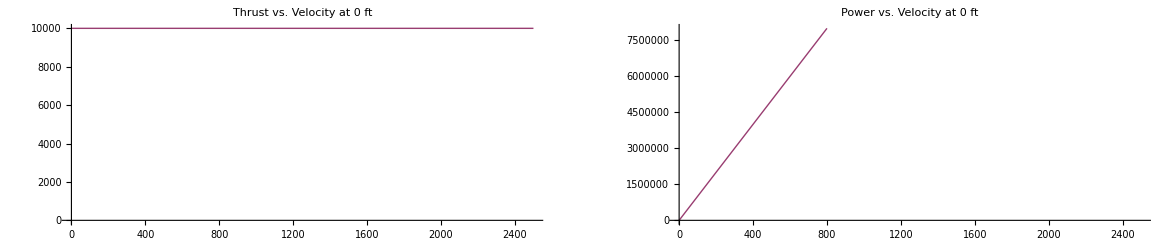

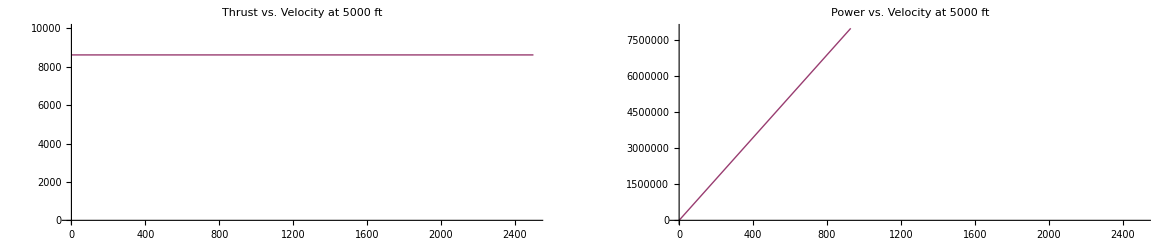

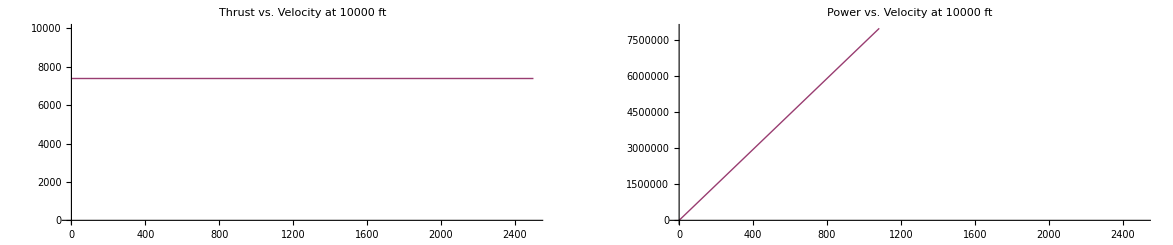

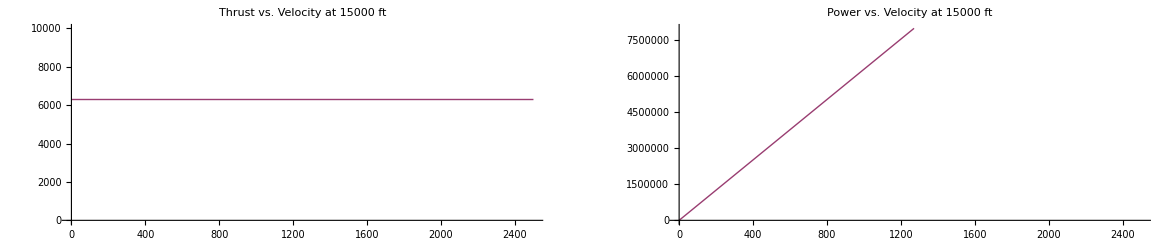

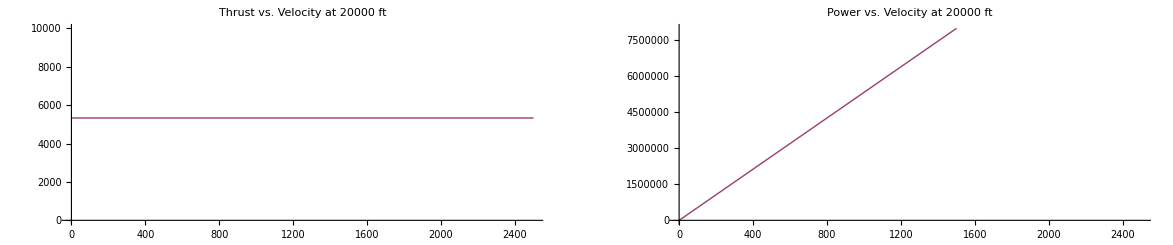

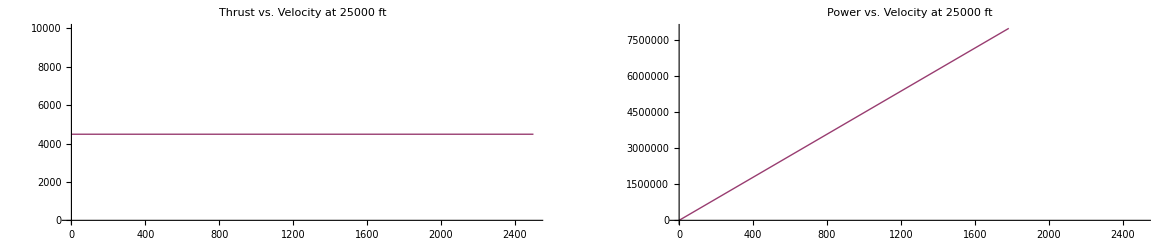

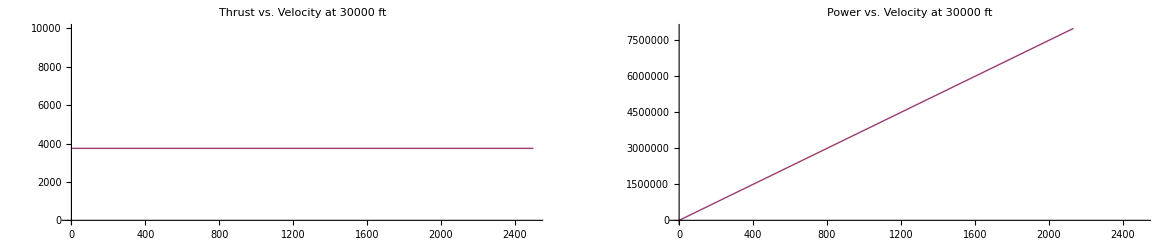

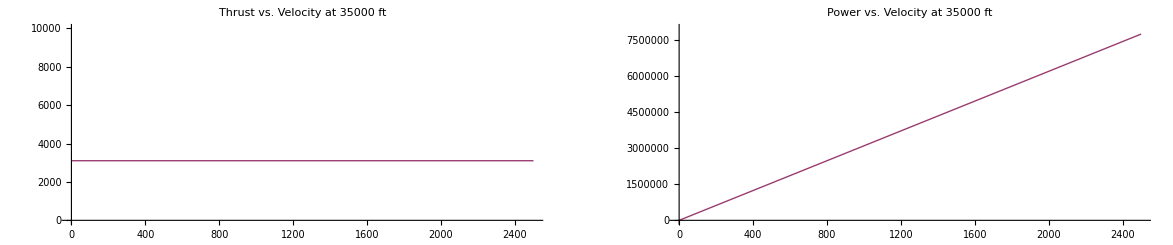

Plot::plln: Limiting value 10 + 7.55717×10^-9\ √7.27989×10^29 + 9.0926×10^8\ Power[« 2 »] - 1.0059×10^-37\ (« 1 »)^3/2\ (0.0172  + 8.51159×10^48\ W0^2/Plus[« 2 »]^2)/W0 in {RC, 0, RCmax[0] + 10} is not a machine-sized real number.

Plot::plln: Limiting value -60000\ (7.55717×10^-9\ √7.27989×10^29 + 9.0926×10^8\ √Plus[« 2 »] - 1.0059×10^-37\ (« 22 » + « 1 »)^3/2\ (0.0172  + 8.51159×10^48\ « 1 »/(« 22 » + « 1 »)^2))/W0\ (-7.55717×10^-9\ √Plus[« 2 »] - 1.0059×10^-37\ « 1 »^« 1 »\ (0.0172  + Times[« 3 »])/W0 + 1.02692×10^-11\ √Plus[« 2 »] - « 1 »/W0) in {A, 0, A[0]} is not a machine-sized real number.

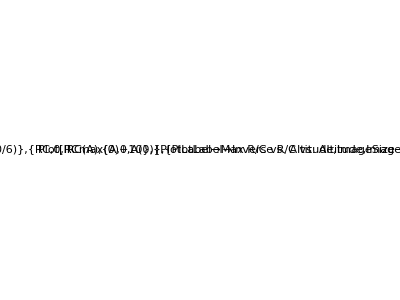

Absolute Ceiling is -(60000 (7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2))))/(W0 (-1/W0(7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2)))+1/W0(1.02692×10^-11 √(3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))-2.79206×10^-44 (3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^(3/2) (0.0172+(2.25665×10^58 W0^2)/((3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^2)))))

Service Ceiling is 100000/(-1/W0(7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2)))+1/W0(1.02692×10^-11 √(3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))-2.79206×10^-44 (3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^(3/2) (0.0172+(2.25665×10^58 W0^2)/((3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^2))))-(60000 (7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2))))/(W0 (-1/W0(7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2)))+1/W0(1.02692×10^-11 √(3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))-2.79206×10^-44 (3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^(3/2) (0.0172+(2.25665×10^58 W0^2)/((3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^2)))))

Combat Ceiling is 500000/(-1/W0(7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2)))+1/W0(1.02692×10^-11 √(3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))-2.79206×10^-44 (3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^(3/2) (0.0172+(2.25665×10^58 W0^2)/((3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^2))))-(60000 (7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2))))/(W0 (-1/W0(7.55717×10^-9 √(7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))-1.0059×10^-37 (7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^(3/2) (0.0172+(8.51159×10^48 W0^2)/((7.27989×10^29+9.0926×10^8 √(6.41023×10^41+1.99519×10^32 W0^2))^2)))+1/W0(1.02692×10^-11 √(3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))-2.79206×10^-44 (3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^(3/2) (0.0172+(2.25665×10^58 W0^2)/((3.56394×10^33+3.73708×10^6 √(9.09487×10^53+3.13148×10^46 W0^2))^2)))))

Plot::plln: Limiting value -60000\ (7.55717×10^-9\ √7.27989×10^29 + 9.0926×10^8\ √Plus[« 2 »] - 1.0059×10^-37\ (« 22 » + « 1 »)^3/2\ (0.0172  + 8.51159×10^48\ « 1 »/(« 22 » + « 1 »)^2))/W0\ (-7.55717×10^-9\ √Plus[« 2 »] - 1.0059×10^-37\ « 1 »^« 1 »\ (0.0172  + Times[« 3 »])/W0 + 1.02692×10^-11\ √Plus[« 2 »] - « 1 »/W0) in {h, 0, A[0]} is not a machine-sized real number.

General::stop: Further output of Plot :: plln will be suppressed during this calculation.

Plot[TimeToClimb[h],{h,0,A[0]},{PlotLabel→TimetoClimb vs. Altitude,ImageSize→Large}]

```mathematica
Aerospace[]
```